## Wprowadzenie do programu MATHEMATICA

## 1. Czyszczenie wszystkich wprowadzonych definicji i podstawień.

### Instrukcja, którą warto umieszczać na początku każdego notebooka:

```mathematica
ClearAll["Global`*"];
```

## 2. Zapis liczb dziesiętnych.

### Liczby dziesiętne zapisujemy z kropką!

```mathematica
3.25
```

3.25

### Zapis liczby dziesiętnej z przecinkiem powoduje pojawienie się komunikatu o błędzie:

```mathematica
3,25
```

## 3. Działania arytmetyczne.

### Dodawanie:

```mathematica
5+7
```

12

```mathematica
Plus[5+7]
```

12

### Odejmowanie:

```mathematica
5-2
```

3

```mathematica
5+Minus[2]
```

3

### Mnożenie:

```mathematica
5*4
```

20

```mathematica
5×4
```

20

```mathematica
5 4
```

20

```mathematica
Times[5,4]
```

20

### Dzielenie:

```mathematica
15/3
```

5

```mathematica
15/3
```

5

```mathematica
Divide[15,3]
```

5

### Potęgowanie:

```mathematica
3^2
```

9

```mathematica
3^2
```

9

```mathematica
Power[3,2]
```

9

## 4. Przybliżenie numeryczne.

```mathematica
6/4
```

3/2

```mathematica
6/4//N
```

1.5

### Przybliżenie numeryczne z podaniem liczby cyfr (w przykładzie 50):

```mathematica
N[π,50]
```

3.1415926535897932384626433832795028841971693993751

## 5. Przypisanie wartości zmiennym.

```mathematica
x=2
(* aktualna wartość x *) x
```

2

2

```mathematica
x=2
x=3
(* aktualna wartość x *) x
```

2

3

3

```mathematica
x=2
x=3
(*Clear[x]*)
(* kasowanie podstawienia.*) x=.
(* aktualna wartość x *) x
```

2

3

x

```mathematica
a+b/. a-> 2
```

2+b

```mathematica
a+b/. {a-> 2,b->5}
```

7

## 6. Korzystanie z palet.

### Palety (menu Palettes) zawierają symbole, które można kopiować do notebooka:

## 7. Wybrane funkcje matematyczne.

### Pierwiastek kwadratowy:

```mathematica
Sqrt[9]
```

3

```mathematica
√9
```

3

### Wartość bezwzględna z liczby:

```mathematica
Abs[-5]
```

5

### Funkcja wykładnicza (eksponencjalna):

```mathematica
Exp[1]
```

ⅇ

```mathematica
ⅇ^1
```

ⅇ

```mathematica
ⅇ^1//N
```

2.71828

### Logarytm naturalny (w przykładzie z e^2):

```mathematica
Log[ⅇ^2]
```

2

### Logarytm dziesiętny (w przykładzie z 1000):

```mathematica
Log10[1000]
```

3

### Logarytm o dowolnej podstawie (w przykładzie o podstawie 7 z 49):

```mathematica
Log[7,49]
```

2

### Funkcja kosinus (w przykładzie dla 20 stopni):

```mathematica
Cos[60Degree]//N
```

0.5

### Funkcja sinus (w przykładzie dla 20 stopni):

```mathematica
Sin[20°]//N
```

0.34202

### Funkcja tangens (w przykładzie dla 20 stopni):

```mathematica
Tan[20°]//N
```

0.36397

### Funkcja kotangens (w przykładzie dla 20 stopni):

```mathematica
Cot[20°]//N
```

2.74748

### Funkcje odwrotne do funkcji trygonometrycznych (w przykładzie dla 1, wartość w radianach):

```mathematica
ArcSin[1]
```

π/2

```mathematica
ArcCos[1]
```

0

```mathematica
ArcTan[1]
```

π/4

```mathematica
ArcCot[1]
```

π/4

## 8. Macierze , listy, wektory.

```mathematica
lista1={5,23,a}
```

{5,23,a}

```mathematica
lista1-2
```

{3,21,-2+a}

```mathematica
lista1×3
```

{15,69,3 a}

```mathematica
lista1/3
```

{5/3,23/3,a/3}

```mathematica
lista1[[1]]
```

5

```mathematica
lista1[[2]]
```

23

```mathematica
lista1[[3]]
```

a

```mathematica
Table[i^2,{i,5}]
```

{1,4,9,16,25}

```mathematica
Table[i,{i,1.3,4.5}]
```

{1.3,2.3,3.3,4.3}

```mathematica
Table[i/2,{i,5.6,20,5}]
```

{2.8,5.3,7.8}

```mathematica
Table[i,{i,5,40,5}]
```

{5,10,15,20,25,30,35,40}

```mathematica
lista2={3,7,12,9,8}
Part[lista2,4]
```

{3,7,12,9,8}

9

```mathematica
Part[lista2,{1,4,5}]
```

{3,9,8}

```mathematica
Part[lista2,-2]
```

9

```mathematica
First[lista2]
```

3

```mathematica
Last[lista2]
```

8

```mathematica
lista3= {2,15,1,4,13}
Take[lista3,3]
```

{2,15,1,4,13}

{2,15,1}

```mathematica
Take[lista3,-2]
```

{4,13}

```mathematica
Drop[lista3,2]
```

{1,4,13}

```mathematica
{1,4,13}
```

{1,4,13}

```mathematica
Drop[lista3,-2]
```

{2,15,1}

```mathematica
Drop[lista3,{2,4}]
```

{2,13}

```mathematica
Prepend[lista3,8]
```

{8,2,15,1,4,13}

```mathematica
Append[lista3,8]
```

{2,15,1,4,13,8}

```mathematica
ReplacePart[lista3,100,3]
```

{2,15,100,4,13}

```mathematica
lista3
```

{2,15,1,4,13}

```mathematica
Cases[{2,15.0,1,-4.0,13},_Integer]
```

{2,1,13}

```mathematica
Cases[{2,15.0,1,-4.0,13},_Real]
```

{15.,-4.}

```mathematica
Cases[{2,15.0,1,-4.0,13},_Real]
```

{15.,-4.}

```mathematica
Cases[{2,15.0,1,-4.0,13},x_ /;x>0]
```

{2,15.,1,13}

```mathematica
Cases[{2,15.0,1,-4.0,13},x_ /;x<0]
```

{-4.}

```mathematica
{2,5,3}+ {-1,3,8}
```

{1,8,11}

```mathematica
{12,9}-{5,2}
```

{7,7}

```mathematica
10×{2,5,3}
```

{20,50,30}

```mathematica
{-3,1,2}.{3,2,4}
```

1

```mathematica
Dot[{-3,1,2},{3,2,4}]
```

1

```mathematica
Cross[{-3,1,2},{3,2,4}]
```

{0,18,-9}

```mathematica
mac2={{2, 5, 0}, {0, 0, 7}, {11, 0, 21}}
```

{{2,5,0},{0,0,7},{11,0,21}}

```mathematica
mac2+2
```

{{4,7,2},{2,2,9},{13,2,23}}

```mathematica
mac1={{1, 3, 0}, {4, 0, 5}, {6, 0, 2}}
```

{{1,3,0},{4,0,5},{6,0,2}}

```mathematica
mac1[[2,3]]
```

5

```mathematica
mac3={{1,3,0},{4,0,5},{6,0,2},{6,0,2}}
```

{{1,3,0},{4,0,5},{6,0,2},{6,0,2}}

```mathematica
mac={{1,3,0},{4,0,5},{6,0,2}}
```

{{1,3,0},{4,0,5},{6,0,2}}

```mathematica
MatrixForm[mac]
```

(1 | 3 | 0
4 | 0 | 5
6 | 0 | 2)

```mathematica
mac1+mac2
```

{{3,8,0},{4,0,12},{17,0,23}}

```mathematica
Map[f,{x,y,z}]
```

{f[x],f[y],f[z]}

```mathematica
Outer[f,{a,b},{c,d}]
```

{{f[a,c],f[a,d]},{f[b,c],f[b,d]}}

```mathematica
Flatten[{8,6, {5,{3,{4,88},8},15}}]
```

{8,6,5,3,4,88,8,15}

```mathematica
{8,6, {5,{3,{4,88},8},15}}// Flatten
```

{8,6,5,3,4,88,8,15}

## 9. Pochodne ( w przykładach po zmiennej x).

```mathematica
D[x^8,x]
```

8 x^7

```mathematica
D[x^n,x]
```

n x^(-1+n)

```mathematica
D[Log[x],x]
```

1/x

```mathematica
D[Sin[x],x]
```

Cos[x]

```mathematica
D[Sin[x]*Cos[x],x]
```

Cos[x]^2-Sin[x]^2

```mathematica
D[x^2*y^3,x]
```

2 x y^3

```mathematica
D[x^8,{x,2}]
```

56 x^6

```mathematica
D[x^n,{x,3}]
```

(-2+n) (-1+n) n x^(-3+n)

```mathematica
D[Log[x],{x,2}]
```

-1/x^2

```mathematica
D[Sin[x],{x,2}]
```

-Sin[x]

```mathematica
D[Sin[x]*Cos[x],{x,3}]
```

-4 Cos[x]^2+4 Sin[x]^2

```mathematica
D[x^2*y^3,x,y]
```

6 x y^2

```mathematica
Dt[x^2*y^3]
```

2 x y^3 Dt[x]+3 x^2 y^2 Dt[y]

```mathematica
Dt[Sin[x]*Cos[y]]
```

Cos[x] Cos[y] Dt[x]-Dt[y] Sin[x] Sin[y]

```mathematica
D[x^8, x]
```

8 x^7

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
D[(x^2*y^3), x,y]
```

6 x y^2

```mathematica
D[x^3, x]
```

3 x^2

```mathematica
D[Log[x], x]
```

1/x

```mathematica
D[(Cos[x]×Sin[x])^4/(x^3+x^2), x]
```

(4 Cos[x]^5 Sin[x]^3)/(x^2+x^3)-((2 x+3 x^2) Cos[x]^4 Sin[x]^4)/((x^2+x^3)^2)-(4 Cos[x]^3 Sin[x]^5)/(x^2+x^3)

```mathematica
D[(x^2*y^3), x]
```

2 x y^3

## 10. Pochodne drugiego rzędu ( w przykładach po zmiennej x).

```mathematica
D[(x^3), x,x]
```

6 x

```mathematica
D[(x^2*y^3), x,x]
```

2 y^3

```mathematica
D[(Cos[x]*y^3), x,x]
```

-y^3 Cos[x]

## 11. Całka nieoznaczona ( w przykładach po zmiennej x).

```mathematica
∫x^n ⅆx
```

x^(1+n)/(1+n)

```mathematica
∫x^2 ⅆx
```

x^3/3

```mathematica
Integrate[x^2,x]
```

x^3/3

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
Integrate[1/x,x]
```

Log[x]

```mathematica
Integrate[Sin[x],x]
```

-Cos[x]

```mathematica
∫D[x^3, x]ⅆx
```

x^3

```mathematica
∫-Sin[x]ⅆx
```

Cos[x]

```mathematica
∫Cos[x]ⅆx
```

Sin[x]

```mathematica
∫1/x ⅆx
```

Log[x]

```mathematica
∫Cos[x]×Sin[x]ⅆx
```

-1/2 Cos[x]^2

```mathematica
∫Cos[x]×Sin[x]ⅆx
```

-1/2 Cos[x]^2

## 12. Całka oznaczona ( w przykładach po zmiennej x).

```mathematica
∫_0^1 x^2 ⅆx
```

1/3

```mathematica
Integrate[x^2,{x,0,1}]
```

1/3

```mathematica
∫_-1^1 x^2 ⅆx
```

2/3

```mathematica
Integrate[x^2,{x,-1,1}]
```

2/3

```mathematica
∫_0^π Cos[x]ⅆx
```

0

```mathematica
Integrate[Cos[x],{x,0,π}]
```

0

```mathematica
∫_0^π Sin[x]ⅆx
```

2

```mathematica
∫_0^(π/2) Cos[x]ⅆx
```

1

```mathematica
∫_0^(π/2) Sin[x]ⅆx
```

1

```mathematica
Integrate[Sin[x],{x,0,π/2}]
```

1

```mathematica
∫_0^(2×π) Cos[x]ⅆx
```

0

```mathematica
∫_0^(2×π) Sin[x]ⅆx
```

0

```mathematica
Integrate[Sin[x],{x,0,2×π}]
```

0

```mathematica
∫_(-π/2)^(π/2) Cos[x]ⅆx
```

2

```mathematica
Integrate[Cos[x],{x,-π/2,π/2}]
```

2

```mathematica
∫_(-π/2)^(π/2) Sin[x]ⅆx
```

0

```mathematica
NIntegrate[Cos[Sin[x]],{x,0,1}]
```

0.86874

```mathematica
Integrate[Cos[Sin[x]],{x,0,1}]
```

∫_0^1 Cos[Sin[x]]ⅆx

## 13. Rozwiązywanie równań ( w przykładach z niewiadomą x).

```mathematica
rown1=Solve[x^2+6==8,x]
```

{{x→-√2},{x→√2}}

```mathematica
(* postać macierzowa zbioru rozwiązań *) MatrixForm[rown1]
```

(x→-√2
x→√2)

## 12. Rozwiązywanie układów równań ( w przykładach z niewiadomymi x oraz y).

```mathematica
rown2=Solve[{x^2+y^2==8,y-2*x==6},{x,y}]
```

{{x→-14/5,y→2/5},{x→-2,y→2}}

```mathematica
(* postać macierzowa zbioru rozwiązań *) MatrixForm[rown2]
```

(x→-14/5 | y→2/5
x→-2 | y→2)

### Podstawienie rozwiązań układu równań “rown2” do nowych zmiennych. Położenie elementu w macierzy wyznacza numer wiersza i numer kolumny w jakich dany element się znajduje:

```mathematica
x1=x/. rown2[[1,1]]
```

-14/5

```mathematica
x2=x/. rown2[[2,1]]
```

-2

```mathematica
y1=y/. rown2[[1,2]]
```

2/5

```mathematica
x2=y/.rown2[[2,2]]
```

2

## 14. Tworzenie wykresów dwuwymiarowych.

### Podstawowa instrukcja (wykres funkcji y = 2 x^2 w przedziale x od -5 do 10):

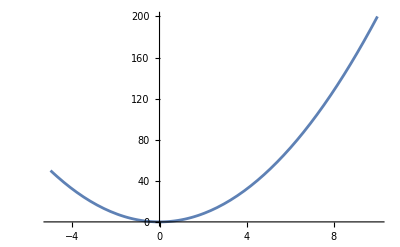

```mathematica
Plot[2*x^2,{x,-5,10}]
```

### Wybieramy czcionkę:

```mathematica
Plot[2*x^2,{x,-5,10},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12}]
```

-Graphics-

### Określamy kolor i grubość wykresu:

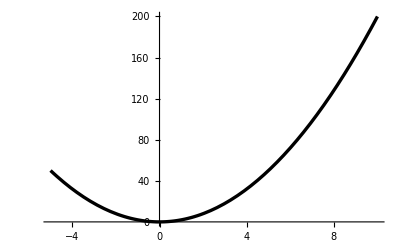

```mathematica
Plot[2*x^2,{x,-5,10},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotStyle->{Black,Thickness[0.006]}]
```

### Dodajemy opis osi:

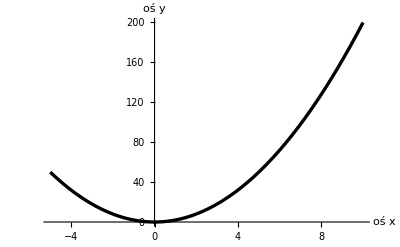

```mathematica
Plot[2*x^2,{x,-5,10},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotStyle->{Black,Thickness[0.006]},AxesLabel->{" oś x"," oś y"}]
```

### Wstawiamy nazwę rysunku:

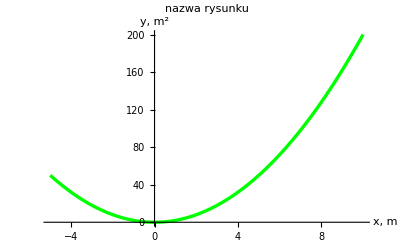

```mathematica
Plot[2*x^2,{x,-5,10},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotStyle->{Green,Thickness[0.006]},AxesLabel->{"x, m","y, m^2"},PlotLabel->"nazwa rysunku"]
```

### Wykres w kolorze czerwonym:

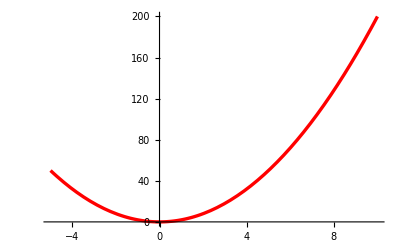

```mathematica
Plot[2*x^2,{x,-5,10},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotStyle->{RGBColor[1,0,0],Thickness[0.006]}]
```

### Dodanie obramowania:

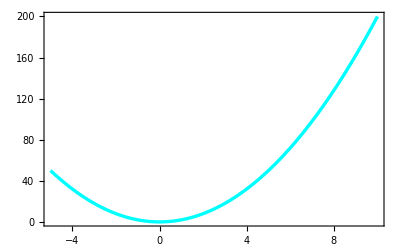

```mathematica
Plot[2*x^2,{x,-5,10},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotStyle->{CMYKColor[1,0,0,0],Thickness[0.006]},Frame->True]
```

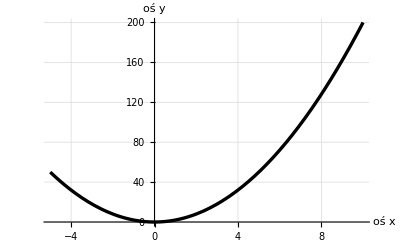

```mathematica
Plot[2*x^2,{x,-5,10},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotStyle->{Black,Thickness[0.006]},AxesLabel->{" oś x"," oś y"},GridLines->Automatic,GridLinesStyle->Directive[Gray]]
```

### Dodanie siatki:

-Graphics-

### Dodanie nazwy rysunku:

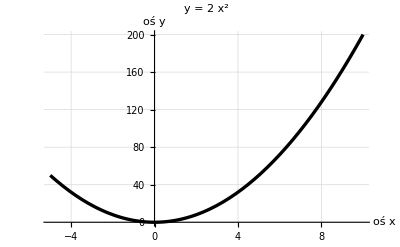

```mathematica
Plot[2*x^2,{x,-5,10},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},PlotStyle->{Black,Thickness[0.006]},AxesLabel->{" oś x"," oś y"},PlotLabel->"y = 2 x^2",GridLines->Automatic,GridLinesStyle->Directive[Gray]]
```

### Sporządzenie dwóch wykresów na jednym rysunku z dodaniem legendy.

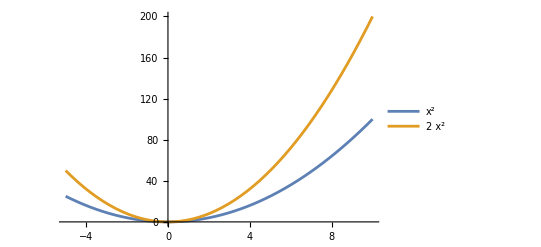

```mathematica
Plot[{x^2,2*x^2},{x,-5,10},PlotLegends->"Expressions"]
```

### Wykorzystanie instrukcji LogLinearPlot, LogPlot oraz LogLogPlot:

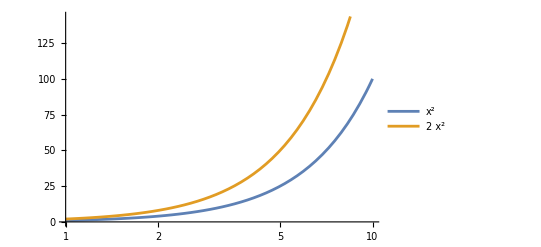

```mathematica
LogLinearPlot[{x^2,2*x^2},{x,1,10},PlotLegends->"Expressions"]
```

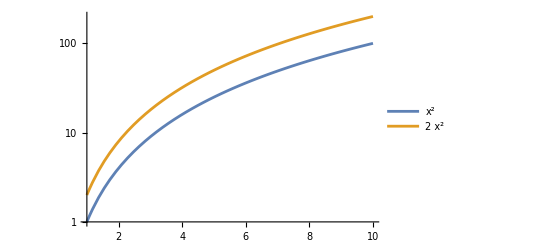

```mathematica
LogPlot[{x^2,2*x^2},{x,1,10},PlotLegends->"Expressions"]
```

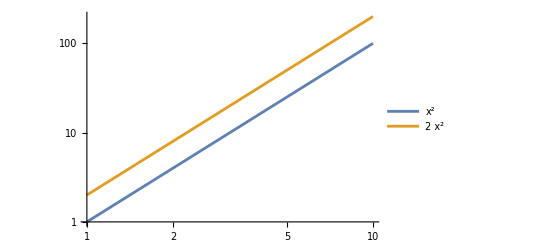

```mathematica
LogLogPlot[{x^2,2*x^2},{x,1,10},PlotLegends->"Expressions"]
```

### Sporządzenie dwóch wykresów na jednym rysunku z wykorzystaniem instrukcji Show.

```mathematica
rysunek1=Plot[x^2,{x,-5,10},PlotStyle->{Black,Thickness[0.006]}];
```

```mathematica
rysunek2=Plot[2*x^2,{x,-5,10},PlotStyle->{Gray,Thickness[0.006]}];
```

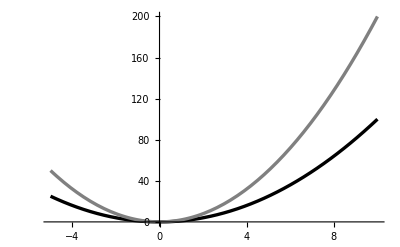

```mathematica
Show[rysunek1,rysunek2,PlotRange->All]
```

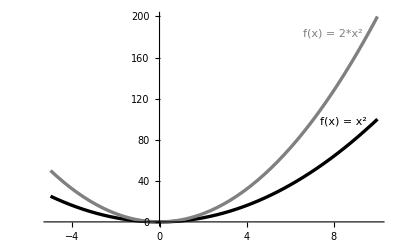

```mathematica
Show[rysunek1,rysunek2,PlotRange->All,Prolog->{Text[StyleForm["f(x) = x^2",FontColor->Black],Scaled[{0.88,0.49}]],
Text[StyleForm["f(x) = 2*x^2  ",FontColor->Gray],Scaled[{0.85,0.90}]]}]
```

## 15. Aproksymacja liniowa danych pomiarowych.

{{1.7,2.1},{3.,4.2},{5.2,5.1},{7.,7.4},{8.,8.4},{9.1,10.5},{11.1,12.},{13.9,14.8},{15.3,17.5},{18.,19.5}}

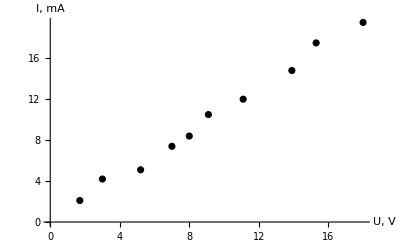

```mathematica
danepomiarowe={{1.7,2.1},{3.0,4.2},{5.2,5.1},{7.0,7.4},{8.0,8.4},{9.1,10.5},{11.1,12.0},{13.9,14.8},{15.3,17.5},{18.0,19.5}}
rysunek1pomiar=ListPlot[danepomiarowe,AxesLabel->{" U, V"," I, mA"},PlotStyle->{Black}]
```

```mathematica
lmod=LinearModelFit[danepomiarowe,{x},x]
```

FittedModel[…]

```mathematica
funaproks[x_]=Normal[lmod]
```

0.175921+1.08062 x

```mathematica
1.08062^-1
```

0.925395

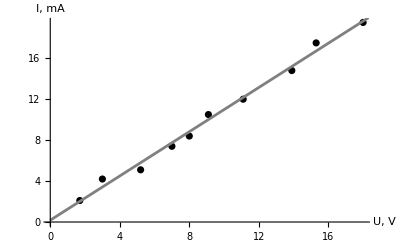

```mathematica
Show[rysunek1pomiar,Plot[funaproks[x],{x,0,20},PlotStyle->{Gray}]]
```

## 16. Wykres parametryczny 2D.

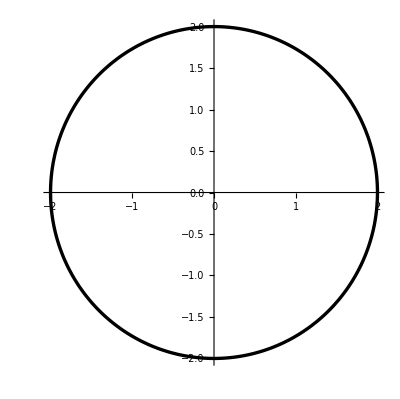

```mathematica
ParametricPlot[{2*Cos[ϕ],2*Sin[ϕ]},{ϕ,0,2* π},PlotStyle->{Black,Thickness[0.006]}]
```

## 17. Wykres trójwymiarowy (3D).

```mathematica
Plot3D[Sin[x+y],{x,-2,2},{y,-2,2},PlotStyle->{Gray},AxesLabel->{" x","y", "sin(x+y)"},PlotLabel->"wykres funkcji f(x) = sin(x+y)"]
```

-Graphics3D-

## 18. Wykres parametryczny 3D.

```mathematica
ParametricPlot3D[{2*Cos[ϕ],2*Sin[ϕ],ϕ/8},{ϕ,0,30},PlotStyle->{Black},AxesLabel->{" x","y", "z"},PlotLabel->" parametryczny wykres trajektorii spiralnej"]
```

-Graphics3D-

## 19.Pętle i instrukcje warunkowe.

```mathematica
Do[Print[i],{i,1,7,2}]
```

1

3

5

7

```mathematica
Do[Print[f[i,j]],{i,1,3,1},{j,1,2,1}]
```

f[1,1]

f[1,2]

f[2,1]

f[2,2]

f[3,1]

f[3,2]

```mathematica
Do[Print[i];Print[i^2];Print[i^3],{i,1,5,2}]
```

1

1

1

3

9

27

5

25

125

```mathematica
Do[Print[MATHEMATICA],{3}]
```

MATHEMATICA

MATHEMATICA

MATHEMATICA

```mathematica
For[i=1,i<= 7,i =  i+2,Print[i]]
```

1

3

5

7

```mathematica
For[i=1,i<= 3,i =  i+1,Print[i]; Print[i^2]]
```

1

1

2

4

3

9

```mathematica
For[i=1,i<= 3,i++,Print[i]; Print[i^2]]
```

1

1

2

4

3

9

```mathematica
i=1;While[i<= 3,Print[i]; Print[i^2];i++]
```

1

1

2

4

3

9

```mathematica
If[2==2,Print[prawda],Print[fałsz],Print[niewiadomo]]
```

prawda

```mathematica
If[3==2,Print[prawda],Print[fałsz],Print[niewiadomo]]
```

fałsz

```mathematica
If[x==2,Print[prawda],Print[fałsz],Print[nie wiadomo]]
```

nie wiadomo

```mathematica
If[2==2,Print[prawda]]
```

prawda

```mathematica
Switch[5+3,5, xx1,8,xx2,2,xx3,2+6,xx4]
```

xx2

```mathematica
Switch[5+3,5, xx1,7,xx2,2,xx3,1+6,xx4]
```

Switch[8,5,xx1,7,xx2,2,xx3,1+6,xx4]

```mathematica
Which[2==5,yy1,3==2,yy2,1==1,yy3, 8==8, yy4]
```

yy3

```mathematica
Which[2==5,yy1,3==2,yy2,1==2,yy3, 7==8, yy4]
```

### Funkcje i procedury.

```mathematica
poleprost[a_,b_]=a*b
```

a b

```mathematica
poleprost[a,b]
```

a b

```mathematica
poleprost[x,y]
```

x y

```mathematica
poleprost[30,50]
```

1500

```mathematica
Clear[poleprost]
```

```mathematica
poleprost[30,50]
```

poleprost[30,50]

```mathematica
suma[a_,b_,c_]:=a+b+c
```

```mathematica
suma[2,3,5]
```

10

```mathematica
wykrespochodnej[g_,h_]:=(f=g*x^3+h*x^2; pochodna=D[f, x];wykres=Plot[pochodna,{x,0,5},PlotStyle->{Black}])
```

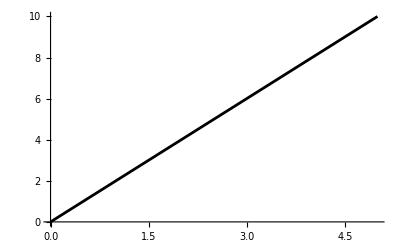

```mathematica
wykrespochodnej[0,1]
```

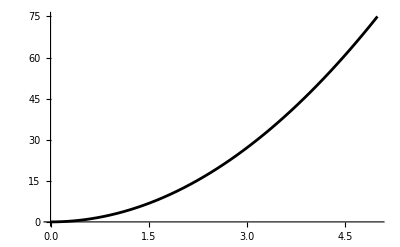

```mathematica
wykrespochodnej[1,0]
```

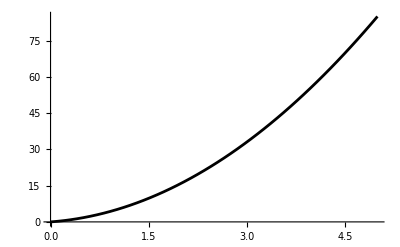

```mathematica
wykrespochodnej[1,1]
```

```mathematica
wykrespochodnej[g_,h_]:=(f=g*x^3+h*x^2; pochodna=D[f, x];wykres=Plot[pochodna,{x,0,5},PlotStyle->{Black}];Return[pochodna])
```

```mathematica
wykrespochodnej[0,1]
```

2 x

```mathematica
wykrespochodnej[1,0]
```

3 x^2

```mathematica
wykrespochodnej[1,1]
```

2 x+3 x^2

## 20. Równania różniczkowe.

```mathematica
DSolve[y''[x]+5*y[x]==0,y[x],x]
```

{{y[x]→C[1] Cos[√5 x]+C[2] Sin[√5 x]}}

```mathematica
DSolve[{y''[x]+5*y[x]==0, y'[0]==5, y[0]==8},y[x],x]
```

{{y[x]→8 Cos[√5 x]+√5 Sin[√5 x]}}

```mathematica
DSolve[{D[y[x], x,x]+5*y[x]==0,D[y[x], x]==5/.x->0,  y[0]==8},y[x],x]
```

{{y[x]→8 Cos[√5 x]+√5 Sin[√5 x]}}

```mathematica
DSolve[{D[y[x],{x,2}]+5*y[x]==0,D[y[x],x]==5/.x->0,  y[0]==8},y[x],x]
```

{{y[x]→8 Cos[√5 x]+√5 Sin[√5 x]}}

```mathematica
DSolve[{y'[x]-2z[x]==Cos[x],y[x]-z[x]==1/2},{y[x],z[x]},x]
```

{{y[x]→ⅇ^(2 x) C[1]+1/10 (5-4 Cos[x]+2 Sin[x]),z[x]→-1/2+ⅇ^(2 x) C[1]+1/10 (5-4 Cos[x]+2 Sin[x])}}

```mathematica
DSolve[D[u[x,y],x]+2D[u[x,y],y]+u[x,y]==5,u[x,y],{x,y}]
```

{{u[x,y]→5+ⅇ^-x C[1][-2 x+y]}}

```mathematica
rownrozn=NDSolve[{y'[x]==y[x]*Sin[x+y[x]],y[0]==3},y[x],{x,0,15}]
```

{{y[x]→InterpolatingFunction[…][x]}}

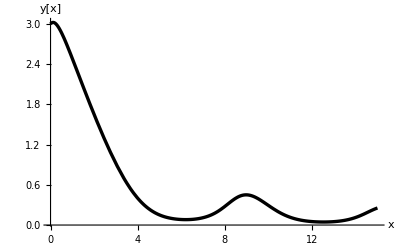

```mathematica
Plot[Evaluate[y[x]/.rownrozn],{x,0,15},PlotStyle->{Black,Thickness[0.006]},AxesLabel->{"x"," y[x]"},PlotRange->All]
```

```mathematica
a=5;
```

```mathematica
b= 50;
```

```mathematica
c=500;
```

```mathematica
Module[{a=3,b=30,c},a+b+c]
```

33+c$31470

```mathematica
Block[{a=3,b=30,c},a+b+c]
```

533

## 21. Stałe fizyczne, jednostki.

```mathematica
Entity["PhysicalConstant","SpeedOfLight"]["Value"]
```

299792458 m/s

```mathematica
Entity["PhysicalConstant", "PlanckConstant"]["Value"]//N
```

6.62607×10^-34 s J

```mathematica
bokkwadratu=Quantity[5,"Meters"]
```

5 m

```mathematica
polekwadratu=bokkwadratu^2
```

25 m^2

```mathematica
Quantity[1,"SpeedOfLight"]
```

c

```mathematica
UnitConvert[Quantity[50,"Meters"],"Kilometers"]//N
```

0.05 km

```mathematica
prsw=UnitConvert[Quantity[1,"SpeedOfLight"]]
```

299792458 m/s

```mathematica
Quantity[1,"Hours"]*prsw
```

1079252848800 m

```mathematica
UnitConvert[Quantity[1,"SpeedOfLight"]]//N
```

2.99792×10^8 m/s

```mathematica
UnitConvert[Quantity[1,"SpeedOfLight"×("Seconds")/("Meters")]]
```

299792458

```mathematica
UnitConvert[Quantity["EarthEquatorialRadius"]]
```

6378137 m

```mathematica
UnitConvert[Quantity[8.2,"Kilometers"],"Meters"]
```

8200. m

```mathematica
UnitConvert[Quantity[1,"Gauss"],"Teslas"]//N
```

0.0001 T

```mathematica
UnitConvert[Quantity[1,"Acres"],"Meters"*"Meters"]//N
```

4046.86 m^2

```mathematica
UnitConvert[Quantity[1,"Webers"],"Gauss"*"Meters"*"Meters"]//N
```

10000. m^2 G

## 22. Operacje wejścia i wyjścia, graficzne obrazowanie danych pomiarowych (instrukcja ListPlot).

```mathematica
(*Directory[]*)
```

```mathematica
(*HomeDirectory[]*)
```

```mathematica
(*ResetDirectory[]*)
```

```mathematica
(*SetDirectory["/home/pd/mathematica/skrypt_pliki"]*)
```

```mathematica
lista=Table[{i,i^2},{i,1,5}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25}}

```mathematica
Export["lista_kwadrat.dat",lista]
```

lista_kwadrat.dat

```mathematica
lista1=ReadList["lista_kwadrat.dat",{Number,Number}]//N
```

{{1.,1.},{2.,4.},{3.,9.},{4.,16.},{5.,25.}}

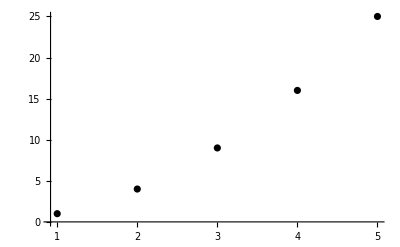

```mathematica
ListPlot[lista1,PlotStyle->Black]
```